```mathematica
SetOptions[EvaluationNotebook[],CommonDefaultFormatTypes->{"Output"->StandardForm}]
```

## Quantum jump in a 2-level system (1)

Review: M. B. Plenio & P. L. Knight, Rev. Mod. Phys. (1998)

    An open quantum system stands as a captivating frontier, where the details of surrounding environment of the relevant system is traced over. Unlike closed systems, open quantum systems engage in a perpetual interaction with their surroundings, exchanging energy, information, and entropy. This interplay gives rise to fascinating phenomena such as decoherence and dissipation, where the delicate quantum coherence of the system is gradually lost to the uncontrollable influences of the environment. This dynamics can be described by various quantum master equations such as Froster theory, Redfield theory, Linblad theory, etc.

    Among those quatum master equation, the Linblad equation can be simulated by the quantum-jump approach. The idea is the realization that the dissipation is induced by the sudden jump between states induced by the random environment interaction. The observed dissipation is obtained from the ensemble average of large amount of repetitive experiments with the same initial state.

    Here we start with a simple free 2-level system as a demonstration of quantum jump approach.

```mathematica
(*intial condition of state |ψ[0]⟩={1,0}*)
Clear[γ,c,t,dt]
γ=1; (*Dimensionless parameter: γ, ℏ=1*)
c={{0,0},{1,0}};(*jumping operator: |1⟩ -> |2⟩*)
t=3;
dt=0.01;
H=-ⅈ/2 γ ConjugateTranspose[c].c;
```

```mathematica
(*** quantum jump iterative algorithm starts here, 1000 replicas ***)
```

```mathematica
Clear[ψ]
Do[
ψ[0,j]={1,0};For[n=0,n≤t/dt,n++,If[Norm[c.ψ[n,j]]^2 dt>RandomReal[{0,1}],ψ[n+1,j]=(c.ψ[n,j])/Norm[c.ψ[n,j]],ψ[n+1,j]=(ψ[n,j]-ⅈ H.ψ[n,j]dt)/Norm[ψ[n,j]-ⅈ H.ψ[n,j]dt]]]
,{j,1,1000}]
Clear[n]
```

```mathematica
(*** the first three quantum jump trajectories ***)
```

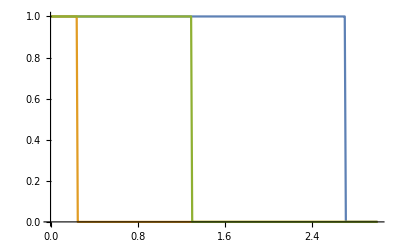

```mathematica
ListPlot[{Table[{n dt,Norm[{1,0}.ψ[n,1]]^2},{n,0,t/dt}],Table[{n dt,Norm[{1,0}.ψ[n,2]]^2},{n,0,t/dt}],Table[{n dt,Norm[{1,0}.ψ[n,3]]^2},{n,0,t/dt}]},Joined->True]
```

Demonstration - 1 
The ensemble average of the first 10 quantum jump trajectories. This shows that the more amount of the repetitive realization in the ensemble, the more dissipative dynamics we capture.

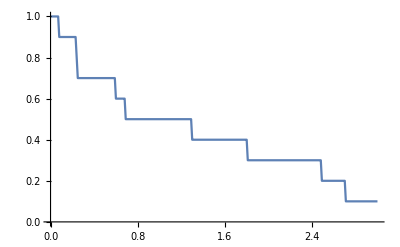

```mathematica
ListPlot[Table[{n dt,Sum[Norm[{1,0}.ψ[n,j]]^2,{j,1,10}]/10},{n,0,t/dt}],Joined->True]
```

Demonstration - 2
The ensemble average of the overall 1000 quantum jump trajectories. This shows that the more amount of the repetitive realization in the ensemble, the more dissipative dynamics we capture.

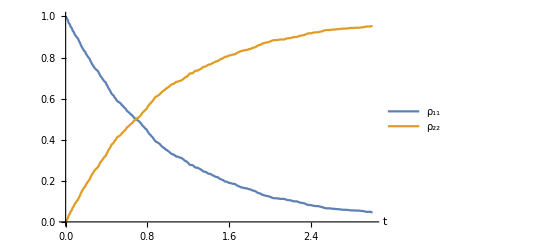

```mathematica
ListPlot[{Table[{n dt,Sum[Norm[{1,0}.ψ[n,j]]^2,{j,1,1000}]/1000},{n,0,t/dt}],Table[{n dt,Sum[Norm[{0,1}.ψ[n,j]]^2,{j,1,1000}]/1000},{n,0,t/dt}]},Joined->True,AxesLabel->{Style["t",FontFamily->"Times New Roman",FontSize->14]},PlotLegends->{Style["ρ_11",FontFamily->"Times New Roman"],Style["ρ_22",FontFamily->"Times New Roman"]}]
```

Demonstration - 3
Here we starts with a general 2-level system with a general initial state by assigning the system Hamiltonian H_0 and the state coefficients a_1 and a_2

```mathematica
Clear[a1,a2,c,t,dt,num,H,H0]
a1=√(2/3);a2=√(1/3); (* intial condition of state |ψ⟩ *)
c={{0,1},{0,0}}; (* jumping operator: |2⟩ -> |1⟩ ; |e⟩ -> |g⟩*)
t=10;dt=0.01;
num=1000; (* sample size of the system / size of the ensemble *)
H0={{0,0},{0,0}};(* system Hamiltonian *)
H=H0-ⅈ/2 ConjugateTranspose[c].c;
```

```mathematica
(*** quantum jump iterative algorithm starts here, 1000 replicas ***)
```

```mathematica
Clear[ψ]
Monitor[Do[
ψ[0,j]={a1,a2};For[n=0,n≤t/dt,n++,If[Norm[c.ψ[n,j]]^2 dt>RandomReal[{0,1}],ψ[n+1,j]=(c.ψ[n,j])/Norm[c.ψ[n,j]],ψ[n+1,j]=(ψ[n,j]-ⅈ H.ψ[n,j]dt)/Norm[ψ[n,j]-ⅈ H.ψ[n,j]dt]]]
,{j,1,num}];,Row[{ProgressIndicator[j,{1,num}],j}," "]]
Clear[n]
```

```mathematica
(*** population dynamics ***)
```

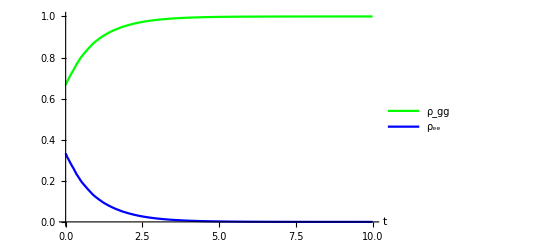

```mathematica
ListPlot[{Table[{n dt,Sum[Norm[{1,0}.ψ[n,j]]^2,{j,1,num}]/num},{n,0,t/dt}],Table[{n dt,Sum[Norm[{0,1}.ψ[n,j]]^2,{j,1,num}]/num},{n,0,t/dt}]},Joined->True,PlotRange->All,PlotStyle->{Green,Blue},AxesLabel->{Style["t",FontFamily->"Times New Roman",FontSize->14]},PlotLegends->{Style["ρ_gg",FontFamily->"Times New Roman"],Style["ρ_ee",FontFamily->"Times New Roman"]}]
```

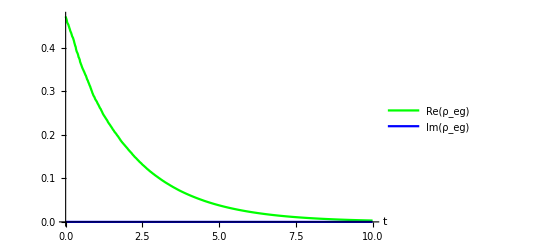

```mathematica
(*** coherent dynamics ***)
ListPlot[{Table[{n dt,Sum[Re[Conjugate[{0,1}.ψ[n,j]]{1,0}.ψ[n,j]],{j,1,num}]/num},{n,0,t/dt}],Table[{n dt,Sum[Im[Conjugate[{0,1}.ψ[n,j]]{1,0}.ψ[n,j]],{j,1,num}]/num},{n,0,t/dt}]},Joined->True,PlotRange->All,PlotStyle->{Green,Blue},AxesLabel->{Style["t",FontFamily->"Times New Roman",FontSize->14]},PlotLegends->{Style["Re(ρ_eg)",FontFamily->"Times New Roman"],Style["Im(ρ_eg)",FontFamily->"Times New Roman"]}]
```

## Quantum jump in cascade system

The same quantum jump approach can be generalized to any quantum system. Here we demonstrate a simple cascade system.

```mathematica
(*intial condition of state |ψ⟩={0,0,1}*)
Clear[c,t,Ω,δ,num,H]
c={{0,1,0},{0,0,1},{0,0,0}}; (*jumping operator: |3⟩ -> |2⟩ -> |1⟩*)
t=20;dt=0.01;
Ω=0.5; (* Rabi freq *)
δ=0.1; (* detuning *)
H0={{0,Ω,0},{Ω,-δ,Ω},{0,Ω,-2δ}};(* system Hamiltonian *)
H=H0-ⅈ/2 ConjugateTranspose[c].c;
num=1000;
```

```mathematica
Clear[ψ]
Monitor[Do[
ψ[0,j]={0,0,1};For[n=0,n≤t/dt,n++,If[Norm[c.ψ[n,j]]^2 dt>RandomReal[{0,1}],ψ[n+1,j]=(c.ψ[n,j])/Norm[c.ψ[n,j]],ψ[n+1,j]=(ψ[n,j]-ⅈ H.ψ[n,j]dt)/Norm[ψ[n,j]-ⅈ H.ψ[n,j]dt]]]
,{j,1,num}];,Row[{ProgressIndicator[j,{1,num}],j},""]]
Clear[n]
```

Demonstration - 1 
The first 3 quantum jump trajectories of the coefficient in state basis |3⟩ and |2⟩. Now the time evolution trajectories of the coefficients themselves are oscillating due to the nontrivial system Hamiltonian.

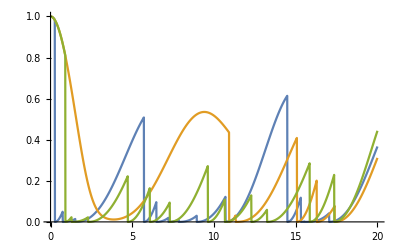

```mathematica
ListPlot[{Table[{n dt,Norm[{0,0,1}.ψ[n,1]]^2},{n,0,t/dt}],Table[{n dt,Norm[{0,0,1}.ψ[n,2]]^2},{n,0,t/dt}],Table[{n dt,Norm[{0,0,1}.ψ[n,3]]^2},{n,0,t/dt}]},Joined->True]
```

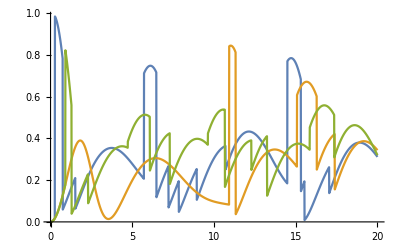

```mathematica
ListPlot[{Table[{n dt,Norm[{0,1,0}.ψ[n,1]]^2},{n,0,t/dt}],Table[{n dt,Norm[{0,1,0}.ψ[n,2]]^2},{n,0,t/dt}],Table[{n dt,Norm[{0,1,0}.ψ[n,3]]^2},{n,0,t/dt}]},Joined->True]
```

Demonstration - 2
The ensemble average of the overall 1000 quantum jump trajectories. This shows that the more amount of the repetitive realization in the ensemble, the more dissipative dynamics we capture.

```mathematica
(*** population dynamics ***)
```

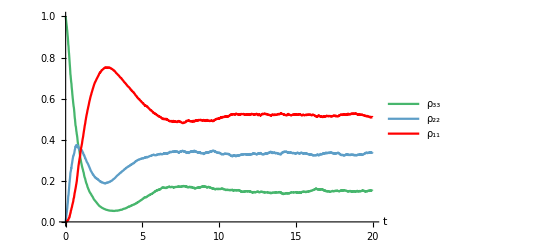

```mathematica
ListPlot[{Table[{n dt,Sum[Norm[{0,0,1}.ψ[n,j]]^2,{j,1,num}]/num},{n,0,t/dt}],Table[{n dt,Sum[Norm[{0,1,0}.ψ[n,j]]^2,{j,1,num}]/num},{n,0,t/dt}],Table[{n dt,Sum[Norm[{1,0,0}.ψ[n,j]]^2,{j,1,num}]/num},{n,0,t/dt}]},Joined->True,PlotRange->All,PlotStyle->{RGBColor[0.28026441037696703,0.715,0.4292089322474965],RGBColor[0.363898,0.618501,0.782349],Red},AxesLabel->{Style["t",FontFamily->"Times New Roman",FontSize->14]},PlotLegends->{Style["ρ_33",FontFamily->"Times New Roman"],Style["ρ_22",FontFamily->"Times New Roman"],Style["ρ_11",FontFamily->"Times New Roman"]}]
```

```mathematica
(*** final population ***)
tn=IntegerPart[t/dt];
Sum[Norm[{0,0,1}.ψ[tn,j]]^2,{j,1,num}]/num
Sum[Norm[{0,1,0}.ψ[tn,j]]^2,{j,1,num}]/num
Sum[Norm[{1,0,0}.ψ[tn,j]]^2,{j,1,num}]/num
Clear[tn]
```

0.151359

0.339459

0.509183

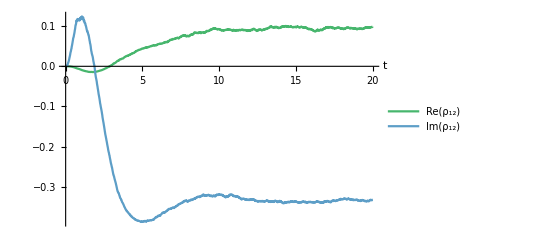

```mathematica
(*** coherent dynamics ***)
ListPlot[{Table[{n dt,Sum[Re[Conjugate[{1,0,0}.ψ[n,j]]{0,1,0}.ψ[n,j]],{j,1,num}]/num},{n,0,t/dt}],Table[{n dt,Sum[Im[Conjugate[{1,0,0}.ψ[n,j]]{0,1,0}.ψ[n,j]],{j,1,num}]/num},{n,0,t/dt}]},Joined->True,PlotRange->All,PlotStyle->{RGBColor[0.28026441037696703,0.715,0.4292089322474965],RGBColor[0.363898,0.618501,0.782349]},AxesLabel->{Style["t",FontFamily->"Times New Roman",FontSize->14]},PlotLegends->{Style["Re(ρ_12)",FontFamily->"Times New Roman"],Style["Im(ρ_12)",FontFamily->"Times New Roman"]}]
```

```mathematica
(*** final coherence ***)
tn=IntegerPart[t/dt];
Sum[Conjugate[{1,0,0}.ψ[999,j]]{0,1,0}.ψ[999,j],{j,1,num}]/num
Clear[tn]
```

0.0927886-0.32003 ⅈ